```mathematica
f[_x] = (x-2)^9
Plot[f, {x, 1.9, 2.1}]
```

(-2+x)^9

-Graphics-

```mathematica
Plot[Simplify[f], {x, 1.9, 2.1}]
```

-Graphics-

```mathematica
f[x_] = (x-2)^9
```

(-2+x)^9

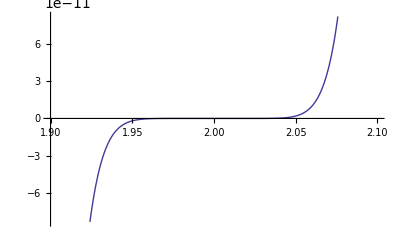

```mathematica
Plot[f[x], {x, 1.9, 2.1}]
```

```mathematica
Simplify[f[x]]
```

(-2+x)^9

```mathematica
Simplify[(x-2)^9]
```

(-2+x)^9

```mathematica
g[x_] = Expand[f[x]]
```

-512+2304 x-4608 x^2+5376 x^3-4032 x^4+2016 x^5-672 x^6+144 x^7-18 x^8+x^9

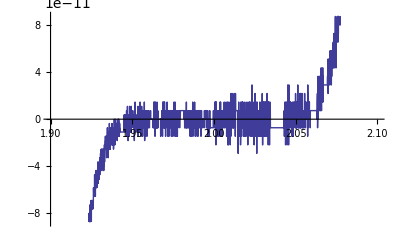

```mathematica
Plot[g[x], {x, 1.9, 2.1}]
```

```mathematica
L0[x_] = ((x-2)*(x-4)*(x-6)) / (-1*-3*-6)
```

-1/18 (-6+x) (-4+x) (-2+x)

```mathematica
L1[x_] = ((x-1)*(x-4)*(x-6)) / (-2*-4)
```

1/8 (-6+x) (-4+x) (-1+x)

```mathematica
L2[x_] = ((x-1)*(x-2)*(x-6)) / (3*2*-2)
```

-1/12 (-6+x) (-2+x) (-1+x)

```mathematica
L3[x_] = ((x-1)*(x-2)*(x-4)) / (5*4*2)
```

1/40 (-4+x) (-2+x) (-1+x)

```mathematica
P[x_] = 2*L0[x] + 9*L1[x] + 41*L2[x] + 97*L3[x]
```

-1/9 (-6+x) (-4+x) (-2+x)+9/8 (-6+x) (-4+x) (-1+x)-41/12 (-6+x) (-2+x) (-1+x)+97/40 (-4+x) (-2+x) (-1+x)

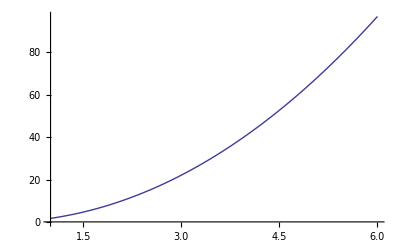

```mathematica
Plot[P[x], {x, 1, 6}]
```

```mathematica
P[x]//Expand
```

-1/15-(46 x)/45+(41 x^2)/15+x^3/45

```mathematica
Plot[Expand[P[x]], {x, 1, 6}]
```

-Graphics-

```mathematica
L0[x_] = ((x-2)*(x-4)*(x-6)) / (-1*-3*-5)
```

-1/15 (-6+x) (-4+x) (-2+x)

```mathematica
P[x_] = 2*L0[x] + 9*L1[x] + 41*L2[x] + 97*L3[x]
```

-2/15 (-6+x) (-4+x) (-2+x)+9/8 (-6+x) (-4+x) (-1+x)-41/12 (-6+x) (-2+x) (-1+x)+97/40 (-4+x) (-2+x) (-1+x)

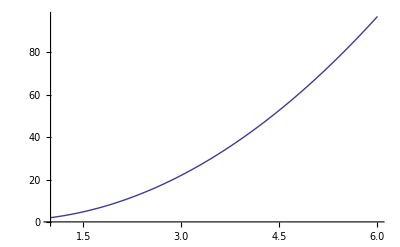

```mathematica
Plot[P[x], {x, 1, 6}]
```

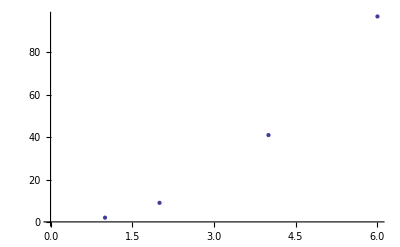

```mathematica
plot1 = ListPlot[{{1,2}, {2,9}, {4, 41}, {6, 97}}]
```

```mathematica
plot2 = Plot[Expand[P[x]], {x, 1, 6}]
```

-Graphics-

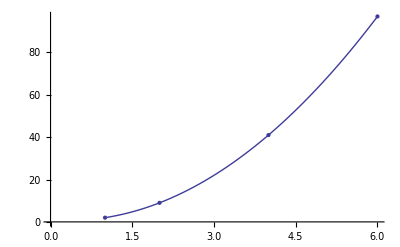

```mathematica
Show[plot1, plot2]
```

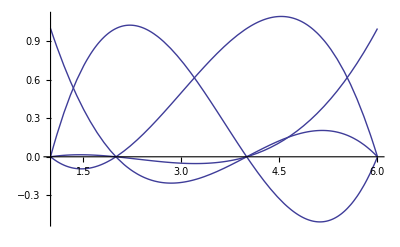

```mathematica
Show[Plot[L0[x], {x, 1, 6}], Plot[L1[x], {x, 1, 6}], Plot[L2[x], {x, 1, 6}], Plot[L3[x], {x, 1, 6}],PlotRange->All]
```

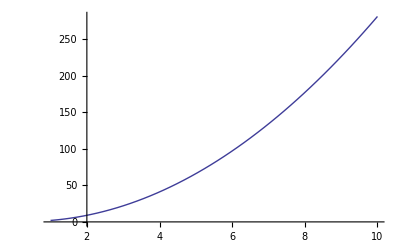

```mathematica
Plot[Expand[P[x]], {x, 1, 10}]
```